The first thing we look at is the potential ψ. We find ψ by first solving for E_g using Gauss’s Law for the charge enclosed in a cylinder. E_gis the gaussian contribution to the radial field E_r. The source for this potential is -(∇^2)_⊥ψ = 4π(ρ - J_z) which is constant in ξ. We are looking at the case with λ_b>λ so the charge involved is λ.

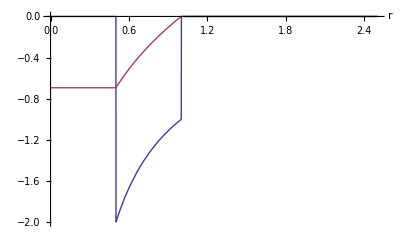

```mathematica
Rs = 0.5;
a =1;
λ = -0.5;
Eg[r_,Rs_] := 2*λ/r*UnitStep[r-Rs] -2*λ/r*UnitStep[r-a];
ψ[r_,Rs_] := 2*λ*Log[a/Rs]-2*λ*Log[r/Rs]*UnitStep[r-Rs]+2*λ*Log[r/a]*UnitStep[r-a];
Needs["PlotLegends`"];
g1=Plot[{Eg[r],ψ[r]},{r,0,2.5},Exclusions->None,PlotRange->All,AxesLabel->Automatic,PlotRangePadding->.1,PlotLegend->{"E_g","ψ"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{0.4,-0.5}]
```

```mathematica
Export["/Users/sgess/Desktop/FACET/hollow_chan/figures/fields_rs_small.pdf",g1,ImageResolution->600];
```

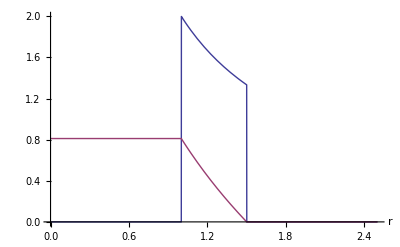

```mathematica
Rs = 1.5;
g2=Plot[{Eg[r],ψ[r]},{r,0,2.5},Exclusions->None,PlotRange->All,AxesLabel->Automatic,PlotRangePadding->.1,PlotLegend->{"E_g","ψ"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{0.4,-0.5}]
```

```mathematica
Export["/Users/sgess/Desktop/FACET/hollow_chan/figures/fields_rs_large.pdf",g2,ImageResolution->600];
```

```mathematica
Animate[Plot[{Eg[r,Rs],ψ[r,Rs]},{r,0,2},Exclusions->None,PlotRange->All],{Rs,0.50,1.4,0.01},AnimationRunning->True]
```

```mathematica
Plot[{Piecewise[{{0,r<Subscript[R, s]},{-2λ/r,r>Subscript[R, s] && r < 1}}],Piecewise[{{2λ*Log[Subscript[R, s]],r<Subscript[R, s]},{2λ*Log[r],r>Subscript[R, s] && r < 1}}]},{r,0,1.5},Exclusions->None,PlotRange->All,AxesLabel->Automatic,PlotRangePadding->.1,PlotLegend->{"E_g","ψ"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{0.4,-0.5}]
```

```mathematica
s=NDSolve[{(1-λ*(1+2Log[r[ξ]]))*r''[ξ]-λ*(r'[ξ])^2*(1/r[ξ]+1) == 0,r[0]==1,r'[0]==-0.005},r,{ξ,0,100}]
```

{{r→InterpolatingFunction[{{0.,100.}},<>]}}

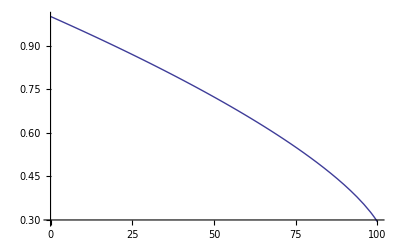

```mathematica
Plot[Evaluate[r[ξ]/.s],{ξ,0,100}]
```